```mathematica
ClearAll["`*"];
```

```mathematica
AppendTo[$Path,"Functions"];
```

```mathematica
<<OpticsFunctions.m
<<GeneralFunctions.m
<<PlotFunctions.m
<<QuantityFunctions.m
<<DataFunctions.m
```

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 287 of "PlotFunctions.m").

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 327 of "PlotFunctions.m").

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 328 of "PlotFunctions.m").

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null.  (line 462 of "PlotFunctions.m").

### Functions

```mathematica
parseKey[keyStr_String]:=StringCases[keyStr,"("~~c1:NumberString~~","~~c2:NumberString~~"),"~~trial:(LetterCharacter|DigitCharacter)..~~",("~~p1:NumberString~~","~~p2:NumberString~~","~~p3:NumberString~~","~~p4:NumberString~~"),"~~d1:NumberString:>{ToExpression[c1],ToExpression[c2],trial,ToExpression/@{p1,p2,p3,p4},ToExpression[d1]}]//First
```

```mathematica
getCyc[keyStr_String]:=StringCases[keyStr,n1:NumberString~~"-"~~n2:NumberString:>{ToExpression[n1],ToExpression[n2]}]//First
getTrial[keyStr_String]:=StringCases[keyStr,n1:NumberString~~"-"~~n2:NumberString~~trial_:>trial]//First
```

```mathematica
ch=<|1->2,2->3,3->4,4->5|>
```

<|1→2,2→3,3→4,4→5|>

```mathematica
coincErr[counts_,factor_:1]:=Around[counts,If[counts!=0,√(factor counts),√factor 1(* (1σ) *)]]
```

```mathematica
coincErr[0]
```

0.00.6

```mathematica
(*Function to read and process a single CSV file*)importHistCSVData[directory_String,cyc1_Integer,cyc2_Integer,trial_String,trigger_Integer, pol_String]:=Module[{fileName,data,columnNames,xValues,histogramData,assoc},
fileName ="cyc("<>ToString[cyc1]<>"-"<>ToString[cyc2]<>")_"<>trial<>"_(";
If[trigger==2,
fileName = fileName<>"b2-b1_a2-a1_b2-a1_a2-b1)_",fileName = fileName<>"b1-b2_a1-a2_a1-b2_b1-a2)_"
];
fileName = fileName<>"pol("<>pol<>").csv";

data=Import[directory<>fileName];
columnNames=First[data];
xValues=Rest[data][[All,1]]/1000; (* nanoseconds *)
histogramData=Transpose[Rest[data][[All,2;;]]];
(*keys = ToString[cyc1]<>"-"<>ToString[cyc2]<>trial<>"trig"<>ToString[trigger]<>pol;*)

(*Return the processed data as an association*)
assoc=<|"x"->xValues|>;
AppendTo[assoc,Rest[columnNames][[#]]->histogramData[[#]]]&/@Range[Length[histogramData]];
assoc
]
```

```mathematica
importHistCSVData[directory_String,cyc1_Integer,cyc2_Integer,trial_String,trigger_Integer, pol_String,centerNS_]:=Module[{fileName,data,columnNames,xValues,histogramData,assoc},
fileName ="cyc("<>ToString[cyc1]<>"-"<>ToString[cyc2]<>")_"<>trial<>"_(";
If[trigger==2,
fileName = fileName<>"bb_aa_ba_ab)_"(*"b2-b1_a2-a1_b2-a1_a2-b1)_"*),fileName = fileName<>"b1-b2_a1-a2_a1-b2_b1-a2)_"
];
fileName = fileName<>"pol("<>pol<>").csv";

data=Import[directory<>fileName];
columnNames=First[data];
xValues=Rest[data][[All,1]]/1000 - centerNS; (* nanoseconds *)
histogramData=Transpose[Rest[data][[All,2;;]]];
(*keys = ToString[cyc1]<>"-"<>ToString[cyc2]<>trial<>"trig"<>ToString[trigger]<>pol;*)

(*Return the processed data as an association*)
assoc=<|"x"->xValues|>;
AppendTo[assoc,Rest[columnNames][[#]]->histogramData[[#]]]&/@Range[Length[histogramData]];
assoc
]
```

```mathematica
importHistCSVData[directory_String,fileName_String,centerNS_:100]:=Module[{data,columnNames,xValues,histogramData,assoc},
data=Import[directory<>fileName];
columnNames=First[data];
xValues=Rest[data][[All,1]]/1000 - centerNS; (* nanoseconds *)
histogramData=Transpose[Rest[data][[All,2;;]]];
(*keys = ToString[cyc1]<>"-"<>ToString[cyc2]<>trial<>"trig"<>ToString[trigger]<>pol;*)

(*Return the processed data as an association*)
assoc=<|"x"->xValues|>;
AppendTo[assoc,Rest[columnNames][[#]]->histogramData[[#]]]&/@Range[Length[histogramData]];
assoc
]
```

```mathematica
rang08=Range[0,8]∪{10};
rang1236=Range[12,18,2]∪Range[24,36,6];
roundToTickList=
rang08∪rang1236∪(10*rang08)∪(10*rang1236)∪(100*rang08);
roundToTickList=roundToTickList∪(-1roundToTickList)
```

{-1000,-800,-700,-600,-500,-400,-360,-300,-240,-200,-180,-160,-140,-120,-100,-80,-70,-60,-50,-40,-36,-30,-24,-20,-18,-16,-14,-12,-10,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,10,12,14,16,18,20,24,30,36,40,50,60,70,80,100,120,140,160,180,200,240,300,360,400,500,600,700,800,1000}

```mathematica
Nearest[roundToTickList,-57][[1]]
```

-60

#### Plot Functions

```mathematica
Unprotect[#]&/@Keys[Options[nlmFitSin4]];
Clear[nlmFitSin4]

Options[nlmFitSin4]= Join[{peakAngle->Null,weightPower->2,includeAdjAngle->False,gridLabels->{"HV","±45°"},labels->""},FilterRules[Options[visListPlot],Except[{labels}]]];
Protect[#]&/@Keys[Options[nlmFitSin2]];

nlmFitSin4[data_Association,opts: OptionsPattern[]]:=nlmFitSin4[Values[data],opts]

nlmFitSin4[data_List,opts: OptionsPattern[]]:=Quiet[Module[{dataLists,amps,vGuesses,peakAngles,weights,fits,fitFuncs,fitsAngle={},fitAngleFuncs={},outputGrid,visPlotOptions,peakAngleO,weightPowerO,includeAdjAngleO,plotAngleStyleO,gridLabelsO,labelsO,plotStyleO},

{peakAngleO,weightPowerO,includeAdjAngleO,gridLabelsO,labelsO,plotStyleO}=OptionValue[{peakAngle,weightPower,includeAdjAngle,gridLabels,labels,plotStyle}];
visPlotOptions=FilterRules[{opts},Except[{peakAngle,weightPower,includeAdjAngle,gridLabels}]];

If[maxDepth[data]<3,
dataLists={data},
dataLists=data];

(*gridLabelsO=SwatchLegend[{plotStyleO[[#]]},{gridLabelsO[[#]]},LegendMarkers->"SphereBubble"]&/@lenRange[dataLists];*)
plotAngleStyleO={#,Thickness[0.006],Opacity[0.6],Dashed}&/@plotStyleO;
plotStyleO={#,Thickness[0.005],Opacity[0.8]}&/@plotStyleO;

amps=Mean[ys[#]]&/@dataLists;
vGuesses=visMaxApprox[#]&/@dataLists;
(*weights=Map[Evaluate[1/yUncerts[#]^weightPowerO]&,dataLists,{2}];*)
weights=1/Evaluate[yUncerts[#]^weightPowerO]&/@dataLists;

peakAngles=safeAccessNum[peakAngleO,#,If[Length[peakAngleO]==0,peakAngleO]]&/@lenRange[dataLists];

fits=If[!MatchQ[peakAngles[[#]],Null],

NonlinearModelFit[onlyValues[dataLists[[#]]],
a(1+v Cos[2(x-peakAngles[[#]])Degree]),
{{a,amps[[#]][[1]]},{v,vGuesses[[#]][[1]]}},x,
Weights->weights[[#]],Method->"LevenbergMarquardt"]
,
NonlinearModelFit[onlyValues[dataLists[[#]]],
a(1+v Cos[2(x-θ)Degree]),
{{a,amps[[#]][[1]]},{v,vGuesses[[#]][[1]]},{θ,15}},x,
Weights->weights[[#]],Method->"LevenbergMarquardt"]

]&/@lenRange[dataLists];

fitFuncs=Normal[#]&/@fits;


If[includeAdjAngleO,
peakAngles=If[!MatchQ[#,Null],#,15]&/@peakAngles;

fitsAngle=NonlinearModelFit[onlyValues[dataLists[[#]]],
a(1+v Cos[2(x-θ)Degree]),
{{a,amps[[#]][[1]]},{v,vGuesses[[#]][[1]]},{θ,peakAngles[[#]]}},x,
Weights->weights[[#]],Method->"LevenbergMarquardt"]&/@lenRange[dataLists];

fitAngleFuncs=Normal[#]&/@fitsAngle;
];


outputGrid=Column[{
ShortVisParameterTable4[fits,gridLabelsO],
If[Length[fitsAngle]>0,ShortVisParameterTable4[fitsAngle,gridLabelsO],{}]
},Spacings->1];

Row[{
Show[visListPlot[dataLists,Sequence@@Join[{labels->labelsO},visPlotOptions]],
Plot[fitFuncs,{x,-100,400},PlotStyle->plotStyleO],
Plot[fitAngleFuncs,{x,-100,400},PlotStyle->plotAngleStyleO]],
outputGrid
},"   "]

],{FittedModel::constr,NonlinearModelFit::lmnl}]
```

```mathematica
datatest={{0,1},{1,0},{3,2},{5,4}, {6,4},{7,5}};
```

```mathematica
nlmtest=NonlinearModelFit[datatest,Log[a +b x^2]+c,{a,b,c},x]
nlmtest2=NonlinearModelFit[datatest,a +c x+b x^2,{a,b,c},x]
```

FittedModel[-0.407109+Log[2.2632+2.14301 x^2]]

FittedModel[0.425069+0.394215 x+0.0398072 x^2]

```mathematica
Flatten[#["ParameterTableEntries"]&/@{nlmtest,nlmtest2},1]
```

{{1.50632,1.10159,1.36741,0.243294},{1.42633,0.600123,2.37673,0.0762602},{0.800399,0.415316,1.9272,0.126221},{0.0933134,0.0153296,6.08714,0.00368246}}

```mathematica
Flatten[Rest[#["ParameterTableEntries"]]&/@{nlmtest,nlmtest2},1]
```

{{1.42633,0.600123,2.37673,0.0762602},{0.0933134,0.0153296,6.08714,0.00368246}}

```mathematica
Flatten[Keys[Rest[#["BestFitParameters"]]]&/@{nlmtest,nlmtest2},1]
```

{b,b}

```mathematica
nlmtest
```

```mathematica
ShortVisParameterTable4[{nlmtest,nlmtest2},{"H/V","±45°"}]
```

Basis | Parameters
H/V | b :  2.1 ±1.2
 | c :  -0.4 ±0.5
±45° | b :  0.04 ±0.07
 | c :  0.4 ±0.5

```mathematica
Column[{
ShortVisParameterTable4[{nlmtest,nlmtest2},{"H/V","±45°"}],
ShortVisParameterTable4[{nlmtest,nlmtest2},{"H/V","±45°"}]
},Spacings->1]
```

Basis | Parameters
H/V | b :  2.1 ±1.2
 | c :  -0.4 ±0.5
±45° | b :  0.04 ±0.07
 | c :  0.4 ±0.5
Basis | Parameters
H/V | b :  2.1 ±1.2
 | c :  -0.4 ±0.5
±45° | b :  0.04 ±0.07
 | c :  0.4 ±0.5

```mathematica
sigFigs[4,0.2]
```

{4.,0.2}

```mathematica
ShortVisParameterTable4[fitmodels_,labels_]:=
Module[{datalist,params,keys,header,vals,num,bases,dividers},
header={"Basis","Parameters"};
params=Flatten[Rest[#["ParameterTableEntries"]]&/@fitmodels,1];
keys=Flatten[Keys[Rest[#["BestFitParameters"]]]&/@fitmodels,1];
num=Length[Rest[fitmodels[[1]]["BestFitParameters"]]];
bases=Table[If[IsDivisible[i/num,1],labels[[Round[i/num]+1]],""],{i,0,Length[keys]-1}];

dividers=Select[Table[If[IsDivisible[i/num,1],i+2->GrayLevel[0.7],""],{i,0,Length[keys]-1}],MatchQ[#,_->_]&];

vals=sigFigs[#[[1]],#[[2]]]&/@params;
vals=sf["`1` ±`2`",#[[1]],#[[2]]]&/@vals;
vals=sf["`1` :  `2`",#[[1]],#[[2]]]&/@Transpose[{keys,vals}];

datalist=Join[{header},Transpose[{bases,vals}]];

Style[Grid[datalist,Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},dividers},Rule[Spacings,{{2->1},{2->0.75}}]],"DialogStyle"]
]
```

```mathematica
IsDivisible[0/3,1]
```

True

```mathematica
IsDivisible//Definition
```

IsDivisible[num1_,num2_,tol_:1/10000000000]:=Module[{quotient},quotient=num1/num2;Abs[Round[quotient]-quotient]<tol]

### Import data

```mathematica
dataMaster=<||>;

(*Define the directory path*)
dir ="sample_data_dualCQMs_spdc_photons"; 

(*Get the list of CSV file paths*)
csvFiles=FileNames["*.csv",dir];

(*Get the filenames from the file paths*)
fileNames=FileNameTake/@csvFiles;

Do[
key= StringCases[filename,"cyc("~~n1:NumberString~~"-"~~n2:NumberString~~")":>"("<>n1<>","<>n2<>")"][[1]];
key=key<>","<>StringCases[filename,"tri("~~trial:WordCharacter..~~")":>trial][[1]];
key=key<>","<>StringCases[filename,"pol("~~p1:NumberString~~","~~p2:NumberString~~","~~p3:NumberString~~","~~p4:NumberString~~")":>"("<>p1<>","<>p2<>","<>p3<>","<>p4<>")"][[1]];
key=key<>","<>StringCases[filename,"dur("~~d1:NumberString~~")":>d1][[1]];
tempData = importHistCSVData[dir,filename];
AppendTo[dataMaster,key->tempData]
,{filename,fileNames}]

visdata=<||>;
visdataDurations=<||>;

cycTime=27;
intRadius=3;

Do[
{c1,c2,tri,pols,dur}=parseKey[key];
(*If[dur<90,Continue[]];*)
ranges=#*cycTime +{-intRadius,intRadius}&/@{0,(c1-c2),c1,-c2};

cycStr=sf["`1`-`2`",c1,c2];

If[StringTake[tri,2]=="ee",
measBasis=Switch[StringTake[tri,{3}],
"1",polB=pols[[1]];polA=pols[[2]];pols[[3]],
"2",polB=pols[[3]];polA=pols[[4]];pols[[1]]]
];


sums=sumPointsWithinRange[cxy[dataMaster[key],ch[#]],ranges[[#]]]&/@lenRange[ranges];


Do[
If[MissingQ[visdata[lvl[[1]]]],
AppendTo[visdata,lvl[[1]]-><||>]
];
If[MissingQ[visdata[lvl[[1]]][lvl[[2]]]],
AppendTo[visdata[lvl[[1]]],lvl[[2]]-><||>]
];
If[MissingQ[visdata[lvl[[1]],lvl[[2]],lvl[[3]]]],
AppendTo[visdata[lvl[[1]],lvl[[2]]],lvl[[3]]-><||>]
];
If[MissingQ[visdata[lvl[[1]],lvl[[2]],lvl[[3]],lvl[[4]]]],
AppendTo[visdata[lvl[[1]],lvl[[2]],lvl[[3]]],lvl[[4]]->{}]
];
,{lvl,{{tri,cycStr,"bb",measBasis},{tri,cycStr,"aa",measBasis},{tri,cycStr,"a1",measBasis},{tri,cycStr,"a2",measBasis}}}];

Do[
If[MissingQ[visdataDurations[lvl[[1]]]],
AppendTo[visdataDurations,lvl[[1]]-><||>]
];
If[MissingQ[visdataDurations[lvl[[1]],lvl[[2]]]],
AppendTo[visdataDurations[lvl[[1]]],lvl[[2]]-><||>]
];
If[MissingQ[visdataDurations[lvl[[1]],lvl[[2]],lvl[[3]]]],
AppendTo[visdataDurations[lvl[[1]],lvl[[2]]],lvl[[3]]->dur]
];
,{lvl,{{tri,cycStr,"bb",measBasis},{tri,cycStr,"aa",measBasis},{tri,cycStr,"a1",measBasis},{tri,cycStr,"a2",measBasis}}}];


AppendTo[visdata[tri,cycStr,"bb",measBasis],{polB,sums[[1]]}];
AppendTo[visdata[tri,cycStr,"aa",measBasis],{polA,sums[[2]]}];
AppendTo[visdata[tri,cycStr,"a1",measBasis],{pols[[2]],sums[[3]]}];
AppendTo[visdata[tri,cycStr,"a2",measBasis],{pols[[4]],sums[[4]]}];

,{key,dataMaster//Keys}]

visdataAndErr=Map[{#[[1]],coincErr[#[[2]]]}&,visdata,{5}];
visdataAndErrPerMin=MapIndexed[{#1[[1]],60*#1[[2]]/visdataDurations[[Sequence@@#2[[;;3]]]]}&,visdataAndErr,{5}];

tempFittedPlot={};
tempFittedPlotPerMin={};
Do[
Do[
Do[

If[MissingQ[visdataAndErr[trial,cycStr,ch]],
Continue[],
If[Length[visdataAndErr[trial,cycStr,ch][[1]]]<4, Continue[]]
];

durMinutes=If[IsDivisible[visdataDurations[trial,cycStr,ch],60],
Round[visdataDurations[trial,cycStr,ch]]/60,
visdataDurations[trial,cycStr,ch]/60.];


If[StringTake[tri,2]=="ee",
measBasis=Switch[StringTake[tri,{3}],
"1",polB=pols[[1]];polA=pols[[2]];pols[[3]],
"2",polB=pols[[3]];polA=pols[[4]];pols[[1]]]
];

tempTitle=Switch[ch,"bb","Before","aa","After",_,ch]<>" Cyc: "<>cycStr(*<> " Trial: "<>trial*);

rools = If[(* the sum of the cycles is even...*)EvenQ[StringCases[cycStr,n1:NumberString~~"-"~~n2:NumberString:>ToExpression[n1]+ToExpression[n2]][[1]]
]||ch=="bb",
{0->90,90->0,45->-45,135->45,-45->45},
{135->-45}
];

angle=Keys[visdataAndErr[trial,cycStr,ch]]/.rools;

tempLegend={"HV","±45°"};

tempAxesLabels={"Measurement Angle","Coinc. per "<>ToString[durMinutes]<>" min"};
tempAxesLabels2={"Measurement Angle","Coinc. per min"};


showAdjAngle=True;

(* nlmFitSin3 limits the visibility from 0 to 1 but this can lead to strange uncertainties
nlmFitSin2 does not limit visibility values 
nlmFitSin4 is the same as 2 but with a more compact data table *)
AppendTo[tempFittedPlot,nlmFitSin4[visdataAndErr[trial,cycStr,ch],peakAngle->angle,includeAdjAngle->showAdjAngle,title->tempTitle,size->260,gridLabels->tempLegend,axesLabels->tempAxesLabels]];
AppendTo[tempFittedPlotPerMin,nlmFitSin4[visdataAndErrPerMin[trial,cycStr,ch],peakAngle->angle,includeAdjAngle->showAdjAngle,title->tempTitle,size->260,gridLabels->tempLegend,axesLabels->tempAxesLabels2]];
,
{cycStr,Flatten[Table[sf["`1`-`2`",c1,c2],{c1,0,10},{c2,0,10}]]}],
{ch,{"bb","aa"(*,"a1","a2"*)}}],
{trial,{"vv","ee1","ee2","ddNoGating","dd1","dd2","dd3","ddT","hh","aa","ad","da","hv","vh"}}]
```

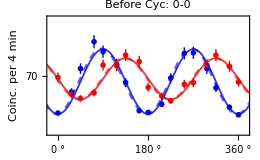
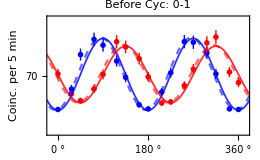
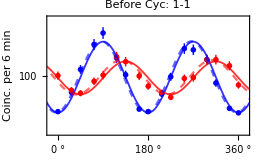
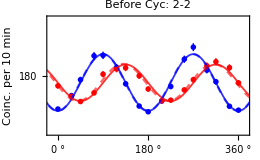
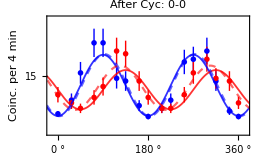
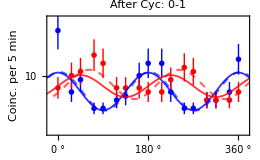
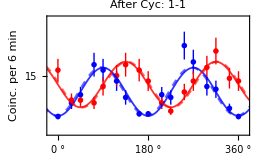
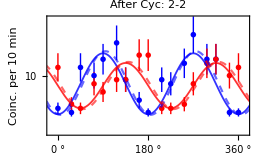
-Graphics-Basis | Parameters
HV | v :  0.93 ±0.03
±45° | v :  0.55 ±0.05
Basis | Parameters
HV | v :  0.93 ±0.03
 | θ :  86.8 ±1.5
±45° | v :  0.55 ±0.05
 | θ :  -47 ±3      -Graphics-Basis | Parameters
HV | v :  0.85 ±0.04
±45° | v :  0.67 ±0.05
Basis | Parameters
HV | v :  0.85 ±0.03
 | θ :  85.2 ±1.2
±45° | v :  0.68 ±0.04
 | θ :  -50.0 ±1.7      -Graphics-Basis | Parameters
HV | v :  0.90 ±0.03
±45° | v :  0.43 ±0.05
Basis | Parameters
HV | v :  0.898 ±0.015
 | θ :  86.5 ±0.9
±45° | v :  0.44 ±0.04
 | θ :  -53 ±3      -Graphics-Basis | Parameters
HV | v :  0.833 ±0.018
±45° | v :  0.54 ±0.04
Basis | Parameters
HV | v :  0.832 ±0.018
 | θ :  89.2 ±1.0
±45° | v :  0.54 ±0.03
 | θ :  -49.7 ±1.6      -Graphics-Basis | Parameters
HV | v :  0.98 ±0.05
±45° | v :  0.73 ±0.10
Basis | Parameters
HV | v :  0.99 ±0.05
 | θ :  93 ±3
±45° | v :  0.77 ±0.07
 | θ :  -56 ±3      -Graphics-Basis | Parameters
HV | v :  0.75 ±0.11
±45° | v :  0.36 ±0.12
Basis | Parameters
HV | v :  0.76 ±0.11
 | θ :  3 ±5
±45° | v :  0.46 ±0.09
 | θ :  63 ±6      -Graphics-Basis | Parameters
HV | v :  0.97 ±0.05
±45° | v :  0.71 ±0.06
Basis | Parameters
HV | v :  0.97 ±0.05
 | θ :  87 ±3
±45° | v :  0.72 ±0.06
 | θ :  -42 ±3      -Graphics-Basis | Parameters
HV | v :  0.93 ±0.08
±45° | v :  0.73 ±0.10
Basis | Parameters
HV | v :  0.95 ±0.08
 | θ :  95 ±4
±45° | v :  0.76 ±0.10
 | θ :  -39 ±5

```mathematica
Row[tempFittedPlot,"\t"]
```

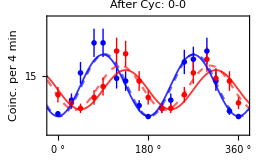
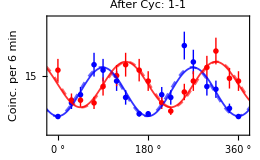
-Graphics- | 
 | Value | σ
a | 60 | ±3
v | 0.93 | ±0.03 |  | Value | σ
a | 65 | ±3
v | 0.55 | ±0.05
 | Value | σ
a | 60 | ±3
v | 0.93 | ±0.03
θ | 86.8 | ±1.5 |  | Value | σ
a | 65 | ±3
v | 0.55 | ±0.05
θ | -47 | ±3      -Graphics- | 
 | Value | σ
a | 72 | ±3
v | 0.85 | ±0.04 |  | Value | σ
a | 72 | ±3
v | 0.67 | ±0.05
 | Value | σ
a | 73 | ±3
v | 0.85 | ±0.03
θ | 85.2 | ±1.2 |  | Value | σ
a | 73 | ±3
v | 0.68 | ±0.04
θ | -50. | ±1.7      -Graphics- | 
 | Value | σ
a | 96 | ±4
v | 0.9 | ±0.03 |  | Value | σ
a | 94 | ±4
v | 0.43 | ±0.05
 | Value | σ
a | 97 | ±3
v | 0.898 | ±0.015
θ | 86.5 | ±0.9 |  | Value | σ
a | 96 | ±3
v | 0.44 | ±0.04
θ | -53 | ±3      -Graphics- | 
 | Value | σ
a | 150 | ±4
v | 0.833 | ±0.018 |  | Value | σ
a | 148 | ±5
v | 0.54 | ±0.04
 | Value | σ
a | 150 | ±4
v | 0.832 | ±0.018
θ | 89.2 | ±1.0 |  | Value | σ
a | 150 | ±4
v | 0.54 | ±0.03
θ | -49.7 | ±1.6      -Graphics- | 
 | Value | σ
a | 11.4 | ±0.9
v | 0.99 | ±0.04 |  | Value | σ
a | 9.8 | ±0.9
v | 0.73 | ±0.10
 | Value | σ
a | 11.5 | ±0.9
v | 0.99 | ±0.04
θ | 93 | ±3 |  | Value | σ
a | 10.5 | ±0.6
v | 0.77 | ±0.07
θ | -56 | ±3      -Graphics- | 
 | Value | σ
a | 6.1 | ±0.6
v | 0.75 | ±0.11 |  | Value | σ
a | 7.4 | ±0.7
v | 0.36 | ±0.12
 | Value | σ
a | 6.2 | ±0.6
v | 0.76 | ±0.11
θ | 3 | ±5 |  | Value | σ
a | 7.8 | ±0.6
v | 0.46 | ±0.09
θ | 63 | ±6      -Graphics- | 
 | Value | σ
a | 9.1 | ±0.7
v | 0.98 | ±0.04 |  | Value | σ
a | 11.7 | ±0.6
v | 0.71 | ±0.06
 | Value | σ
a | 9.1 | ±0.7
v | 0.98 | ±0.04
θ | 87 | ±3 |  | Value | σ
a | 11.7 | ±0.6
v | 0.72 | ±0.06
θ | -42 | ±3      -Graphics- | 
 | Value | σ
a | 8. | ±0.9
v | 0.93 | ±0.08 |  | Value | σ
a | 7.6 | ±0.7
v | 0.73 | ±0.10
 | Value | σ
a | 8.2 | ±0.9
v | 0.95 | ±0.08
θ | 95 | ±4 |  | Value | σ
a | 7.6 | ±0.7
v | 0.76 | ±0.10
θ | -39 | ±5

```mathematica
Row[tempFittedPlot,"\t"]
```

```mathematica
nb=CreateDocument[];(*Create a new,empty notebook*)
NotebookWrite[nb,Cell[BoxData[ToBoxes[
Grid[
Transpose[{tempFittedPlot[[;;4]],tempFittedPlot[[-4;;]]}],
ItemSize->All,Spacings->{2,2}
]
]],"Output"]]
```

```mathematica
nb=CreateDocument[];(*Create a new,empty notebook*)
NotebookWrite[nb,Cell[BoxData[ToBoxes[Row[tempFittedPlot,"\t"]]],"Output"]]
```